```mathematica
SizedDots[n_]:= Table[ Directive[PointSize[0.05*(n+1-i)/n],Hue[i/n]],{i,n}]
```

# Manifolds

## Manifolds: Definitions

The formal definition of the stable manifold of a hyperbolic fixed point p of a map F:ℝ^m→ℝ^m is easy to state
	S_p={q∈ℝ^m:q->p under the map F}
For an invertible map F the definition of the unstable manifold is just about as simple
	U_p={q∈ℝ^m:q->p under the map F^-1}
Both definitions hide quite a lot of detail.

### Manifolds Visualization: version one

The tools we have fro the Henon map are

```mathematica
F[a_,b_][{x_,y_}]:={1- a x^2 + y, b x}
DF[a_,b_][{x_,y_}]:={{-2 a x,1},{b,0}}
FInv[a_,b_][{x_,y_}]:= {y/b, -1+x + a y^2/b^2}
FixedPts[a_,b_]:={
{-(1-b+√(1+4 a-2 b+b^2))/(2 a),1/2 (-b/a+b^2/a-(b √(1+4 a-2 b+b^2))/a)},{(-1+b+√(1+4 a-2 b+b^2))/(2 a),1/2 (-b/a+b^2/a+(b √(1+4 a-2 b+b^2))/a)}}
```

Here is version one.  It might be good enough to see what is going on.

#### ++ Fixed Point: Unstable Manifold!

Lets “sketch” the unstable manifold at the second fixed point: the one with the plus.

General::munfl: (-0.0699996)^267 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.0699996)^268 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.0699996)^269 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

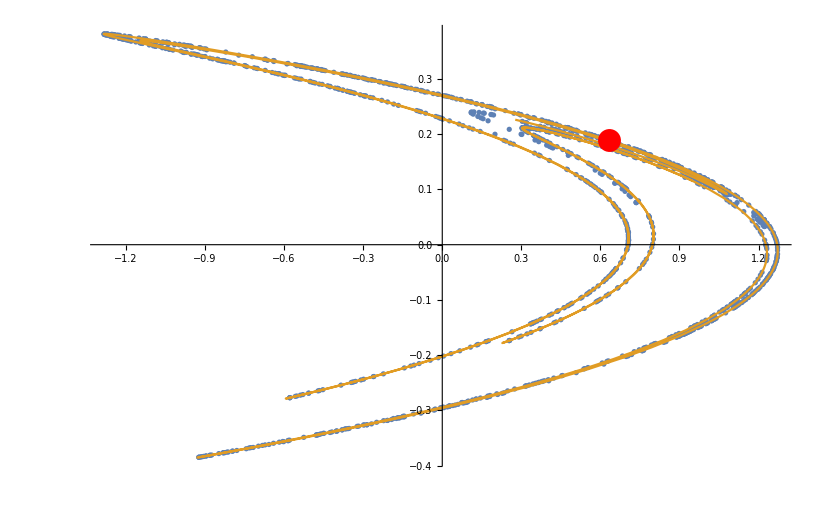

```mathematica
{a,b}={1.4,0.3};
{p,q}=FixedPts[a,b];
{{λ2,λ1},{v2,v1}}=Eigensystem[DF[a,b][q]];
MaxIter=9;
Mani[τ_]=Expand[Nest[F[a,b],q + τ v2 ,MaxIter]];
h=0.07;
SManQ=Show[
ListPlot[ NestList[F[a,b], {0.2,0.2},1234]],
ParametricPlot[{q + τ v2,Mani[τ]},
{τ,-h, h},
PlotRange->All,
PlotPoints->400,
MaxRecursion->7],
Epilog->{Red, PointSize[0.02],Point[q]}
]
```

#### ++ Fixed Point: Stable Manifold!

Lets “sketch” the stable manifold at the second fixed point: the one with the plus.

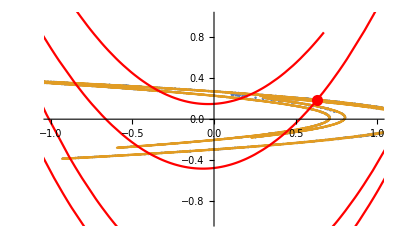

```mathematica
{a,b}={1.4,0.3};
{p,q}=FixedPts[a,b];
{{λ2,λ1},{v2,v1}}=Eigensystem[DF[a,b][q]];
MaxIter=4;
Mani[τ_]=Expand[Nest[FInv[a,b],q + τ v1 ,MaxIter]];
h=0.1;
UManQ=ParametricPlot[Mani[τ],
{τ,-h, h},
PlotStyle->Red,
PlotRange->All,
PlotPoints->400,
MaxRecursion->7,
Epilog->{Red, PointSize[0.02],Point[q]}];
Show[ SManQ, UManQ,
PlotRange->{{-1,1},{-1,1}}]
```

#### +- Fixed Point: Unstable and Stable Manifold!

Lets “sketch” the stable and unstable manifolds at the first fixed point: the one with the minus.

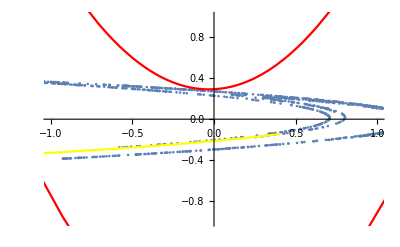

```mathematica
{a,b}={1.4,0.3};
{p,q}=FixedPts[a,b];
{{λ2,λ1},{v2,v1}}=Eigensystem[DF[a,b][p]];
MaxIter=3;
UMani[τ_]=Expand[Nest[F[a,b],p + τ v2 ,MaxIter]];
SMani[τ_]=Expand[Nest[FInv[a,b],p + τ v1 ,MaxIter]];
h=0.07;
SManQ=Show[
ListPlot[ NestList[F[a,b], {0.2,0.2},1234]],
ParametricPlot[SMani[τ],
{τ,-h, h},
PlotRange->All,
PlotStyle->Red,
PlotPoints->400,
MaxRecursion->7],
ParametricPlot[UMani[τ],
{τ,-h, h},
PlotRange->All,
PlotPoints->400,
PlotStyle->Yellow,
MaxRecursion->7],
Epilog->{Red, PointSize[0.02],Point[p]},
PlotRange->{{-1,1},{-1,1}}
]
```

## Manifold: Weirdness